```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/guo/Dropbox/Work/singularities

## Numerics

```mathematica
<<HadronMasses`
MLambdab=5.6195;
Needs["ErrorBarPlots`"]
```

```mathematica
phasespace[M_,m1_,m2_,m3_,m12_]:=With[{p1star=qcm[m12,m1,m2],p3=qcm[M,m12,m3]},p1star*p3]
ps[m12_]:=phasespace[MJ,mpi0,mphi,meta,m12]
```

```mathematica
Install["C:\\cygwin\\bin\\LoopTools.exe"] //Quiet
```

LinkObject[…]

```mathematica
Install["LoopTools"] //Quiet
```

LinkObject[/home/guo/.Mathematica/Applications/LoopTools,188,4]

```mathematica
?C0i
```

C0i[id, p1, p2, p1p2, m1, m2, m3] is the generic three-point loop integral which includes both scalar and tensor coefficients, specified by id.  C0i[cc0, ...] is the scalar function C_0, C0i[cc112, ...] the tensor coefficient function C_112 etc.  p1, p2, and p1p2 are the external momenta squared and m1, m2, m3 are the masses squared.

```mathematica
C0[3^2,0.1^2,2^2,1.5^2,2^2,1^2]
C0i[cc0,3^2,0.1^2,2^2,1.5^2,2^2,1^2]
```

-0.461843

-0.461843

```mathematica
(* relativistic three-point scalar loop from LoopTools, corresponding to J in the above *)
LoopToolsJ[m1_,m2_,m3_,M_,Mh_,ml_]:=-(C0[M^2,ml^2,Mh^2,m2^2,m1^2,m3^2]*m1*m2*m3)/(16*Pi^2)
LoopToolsI1[id_:cc2,m1_,m2_,m3_,M_,Mh_,ml_]:=-(C0i[id,M^2,ml^2,Mh^2,m2^2,m1^2,m3^2]*m1*m2*m3)/(16*Pi^2)
```

```mathematica
thick=Thickness[0.0036];
morethick=Thickness[0.004];
aspect=2./3 (*(√5-1)/2.*);
gray=Lighter[Gray,0.7];
font=Sequence@@{FontSize->16,FontFamily->"Times"};
font1=Sequence@@{FontSize->14,FontFamily->"Times"};
font2=Sequence@@{FontSize->14,FontFamily->"Arial"};
blue=Lighter[Blue,0.6];
```

```mathematica
LandauEquation[m1_,m2_,m3_,mL_,M_,Mh_]:=Module[{p1sq,p2sq,p3sq,y1,y2,y3,eq,sol},p3sq=M^2;
p2sq=mL^2;
p1sq=Mh^2;
y1=(m2^2+m3^2-p1sq)/(2 m2 m3);
y2=(m1^2+m3^2-p2sq)/(2 m1 m3);
y3=(m1^2+m2^2-p3sq)/(2 m1 m2);
eq=1+2 y1 y2 y3-y1^2-y2^2-y3^2]
(* q_(on+)=q_(a-) *)
RelevantSingularity[m1_,m2_,m3_,mL_,M_,m23_]:=Module[{qon,k,gamma,gabeta,p2star,e2star,qaminus,eq},qon=qcm[M,m1,m2];
k=qcm[M,m23,mL];
gabeta=k/m23;
gamma=Sqrt[k^2+m23^2]/m23;
p2star=qcm[m23,m2,m3];
e2star=(m23^2+m2^2-m3^2)/(2 m23);
qaminus=gabeta*e2star-gamma*p2star;
eq=qon-qaminus
]
m1sqlow[m2_,m3_,mL_,M_]:=(M^2 m3-m2^2 m3-m2 m3^2+m2 mL^2)/(m2+m3)
m1sqhigh[m2_,M_]:=(M-m2)^2
m1range[m2_,m3_,ml_,M_]:={√m1sqlow[m2,m3,ml,M],M-m2}
```

```mathematica
cos[E1_,E3_,m1_,m2_,m3_,s_]:=(√((2 E1 E3 -2 Sqrt[s](E1+E3)+s+m1^2-m2^2+m3^2)^2))/(2 √((E1^2-m1^2)(E3^2-m3^2)))

coss[s12_,s23_,m1_,m2_,m3_,s_]:=cos[(s+m1^2-s23)/(2 Sqrt[s]),(s+m3^2-s12)/(2 Sqrt[s]),m1,m2,m3,s]
```

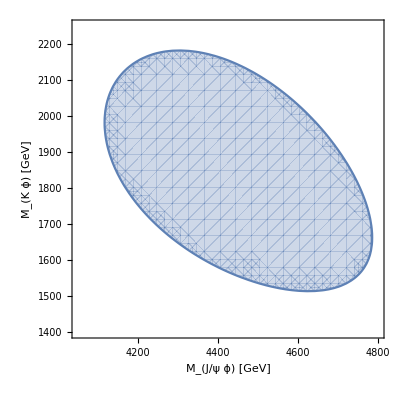

```mathematica
RegionPlot[{coss[m12^2,m23^2,mkc*1000,mphi*1000,MJ*1000,(MBc*1000)^2]≤1},{m23,4050,4800},{m12,1400,2250},
MeshStyle->{Blue,Orange},
FrameLabel->{"M_(J/ψ ϕ) [GeV]","M_(K ϕ) [GeV]"}]
```

```mathematica
√{m1sqlow[2.7,MDs,mkc,MBc],m1sqhigh[2.7,MBc]}
```

{2.56464,2.57917}

```mathematica
NSolve[RelevantSingularity[m1,m2,m3,ml,M,mh]==0./.{m1->2.569,m2->#1,m3->#2,ml->mkc,M->MBc},mh]&[2.708,MDs]
```

{{mh→5.65329×10^8},{mh→-5.65329×10^8},{mh→4.68158},{mh→-4.68158},{mh→0.+1.3376×10^-8 ⅈ},{mh→0.-1.3376×10^-8 ⅈ}}

```mathematica
√{m1sqlow[2.56,MDs,mkc,MBc],m1sqhigh[2.56,MBc]}
```

{2.68572,2.71917}

```mathematica
NSolve[RelevantSingularity[m1,m2,m3,ml,M,mh]==0./.{m1->2.569,m2->#1,m3->#2,ml->mkc,M->MBc},mh]&[2.56,MDs]
```

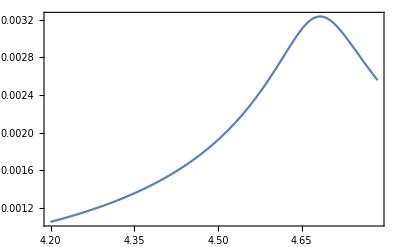

```mathematica
(* triangle singularity in B->K+(e.g.,J/ψω) *)
Plot[Evaluate[Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->2.564-ⅈ 0.07,m2->2.708-ⅈ 0.06,m3->MDs,ml->mkc,M->MBc})^2],{mx,4.2,4.8},PlotRange->All,Frame->True]
```

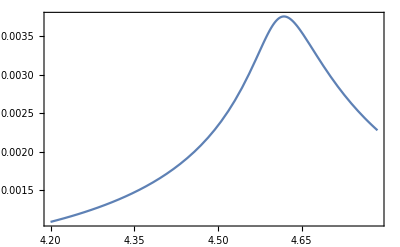

```mathematica
(* triangle singularity in B->K+(e.g.,J/ψω) *)
Plot[Evaluate[Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->2.569-ⅈ 0.08,m2->2.737-ⅈ 0.04,m3->MDc,ml->mkc,M->MBc})^2],{mx,4.2,4.8},PlotRange->All,Frame->True]
```

```mathematica
NSolve[LandauEquation[m1,m2,m3,ml,M,mh]==0./.{m2->#1,m3->#2,ml->mkc,mh->4.14,M->MBc},m1]&[MDs,MDstars]
NSolve[RelevantSingularity[m1,m2,m3,ml,M,mh]==0./.{m2->#1,m3->#2,ml->mkc,mh->4.63,M->MBc},m1]&[2.7,MDs]
```

{{m1→-3.30778},{m1→3.30778},{m1→3.05205},{m1→-3.05205}}

{{m1→7.97492-0.0166867 ⅈ},{m1→-7.97492+0.0166867 ⅈ},{m1→2.59284+0.051324 ⅈ},{m1→-2.59284-0.051324 ⅈ}}

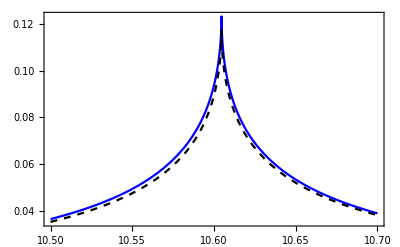

```mathematica
Plot[{Evaluate[Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->5.535-ⅈ 0.113,m2->MBstar,m3->MB0,ml->mpic,M->MUps5S})^2],
Evaluate[Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->5.584-ⅈ 0.119,m2->MB0,m3->MBstar,ml->mpic,M->MUps5S})^2]},{mx,10.5,10.7},PlotRange->All,Frame->True,PlotStyle->{{Blue},{Dashed,Black}}]
```

### J/ψ→π^0 ϕ η

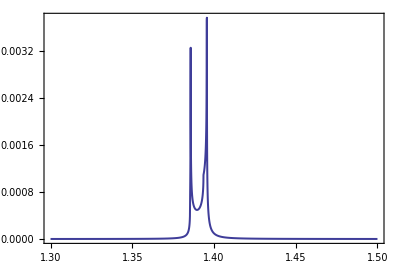

```mathematica
(* check whether the scalar 3-point loop integral gives the expected behavior. here plotted is the difference between the neutral and charged loop integrals *)
Plot[Evaluate[Abs@((LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})
-(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc,m2->mkc,m3->mkc,ml->mpi0,mx->mphi}))^2],{M,1.3,1.5},PlotRange->All,Frame->True]
```

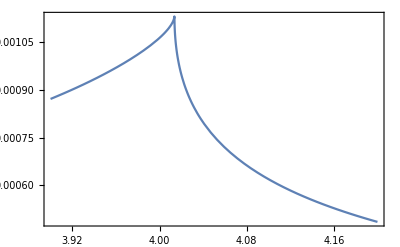

```mathematica
Plot[Evaluate[Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->2.536-ⅈ #,m2->MDstar0,m3->MDstar0,ml->mk0,M->MB0})^2]&[0.00024],{mx,3.9,4.2},PlotRange->All,Frame->True]
```

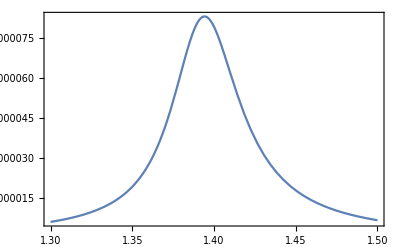
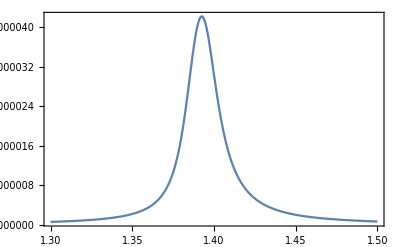
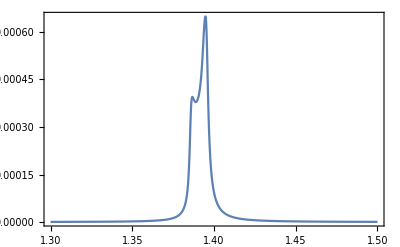

```mathematica
(* check the effect of the K^* width: from top to bottom, the width is 48 MeV, 20 MeV and 2 MeV, respectively *)
{Plot[Evaluate[Abs@((LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})
-(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi}))^2]&[0.024],{M,1.3,1.5},PlotRange->All,Frame->True],
Plot[Evaluate[Abs@((LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})
-(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi}))^2]&[0.01],{M,1.3,1.5},PlotRange->All,Frame->True],
Plot[Evaluate[Abs@((LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})
-(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi}))^2]&[0.001],{M,1.3,1.5},PlotRange->All,Frame->True]}
```

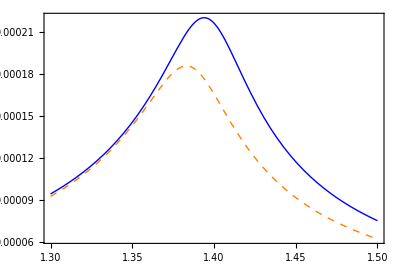
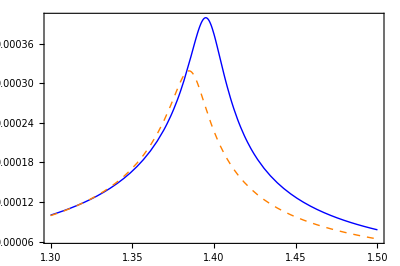
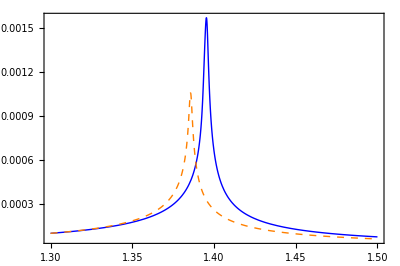

```mathematica
(* check the neutral and charged scalar 3-point loops independently. Blue-solid: neutral; Orange-dashed: charged *)
{Plot[Evaluate[{Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})^2,
Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})^2}&[0.024]],{M,1.3,1.5},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}],
Plot[Evaluate[{Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})^2,
Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})^2}&[0.01]],{M,1.3,1.5},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}],
Plot[Evaluate[{Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})^2,
Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})^2}&[0.001]],{M,1.3,1.5},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}]}
```

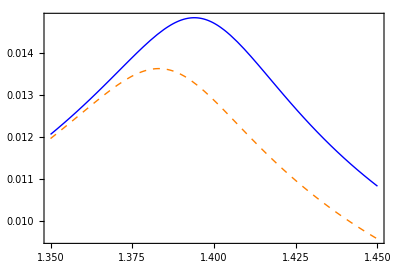
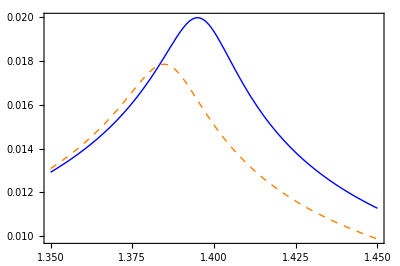
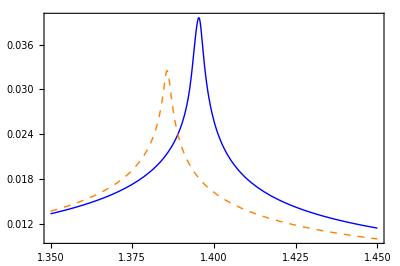

```mathematica
(* check the neutral and charged scalar 3-point loops independently. Blue-solid: neutral; Orange-dashed: charged *)
plot0={Plot[Evaluate[{Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi}),
Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})^1}&[0.024]],{M,1.35,1.45},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}],
Plot[Evaluate[{Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi}),
Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})^1}&[0.01]],{M,1.35,1.45},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}],
Plot[Evaluate[{Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi}),
Abs@(LoopToolsJ[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})}&[0.001]],{M,1.35,1.45},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}]}
```

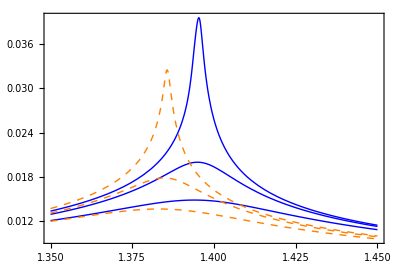

```mathematica
Show[plot0]
```

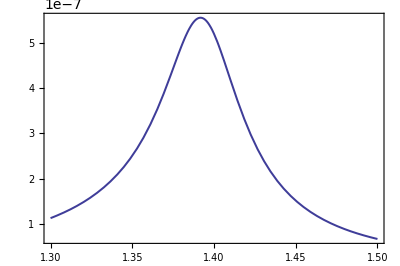
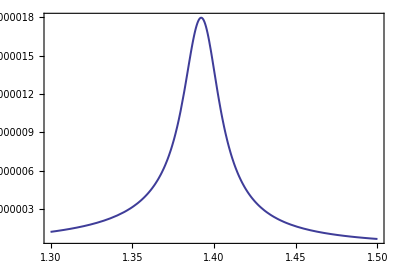
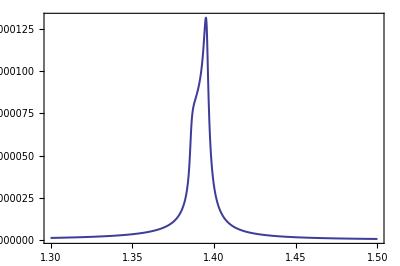

```mathematica
(* check the the TS behavior using one of the vector 3-point loop integral including the effect of the K^* width: from top to bottom, the width is 48 MeV, 20 MeV and 2 MeV, respectively *)
{Plot[Evaluate[Abs@((LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})
-(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi}))^2]&[0.024],{M,1.3,1.5},PlotRange->All,Frame->True],
Plot[Evaluate[Abs@((LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})
-(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi}))^2]&[0.01],{M,1.3,1.5},PlotRange->All,Frame->True],
Plot[Evaluate[Abs@((LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})
-(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi}))^2]&[0.001],{M,1.3,1.5},PlotRange->All,Frame->True]}
```

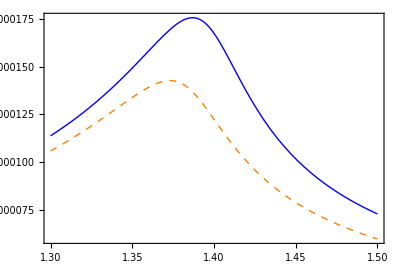
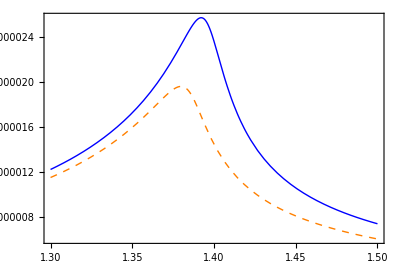
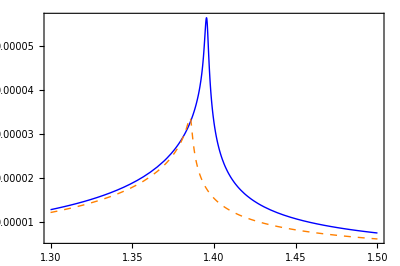

```mathematica
(* check the neutral and charged scalar 3-point loops independently. Blue-solid: neutral; Orange-dashed: charged *)
{Plot[Evaluate[{Abs@(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})^2,
Abs@(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})^2}&[0.024]],{M,1.3,1.5},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}],
Plot[Evaluate[{Abs@(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})^2,
Abs@(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})^2}&[0.01]],{M,1.3,1.5},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}],
Plot[Evaluate[{Abs@(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstar0-ⅈ #,m2->mk0,m3->mk0,ml->mpi0,mx->mphi})^2,
Abs@(LoopToolsI1[m1,m2,m3,M,mx,ml]/.{m1->mkstarc-ⅈ #,m2->mkc,m3->mkc,ml->mpi0,mx->mphi})^2}&[0.001]],{M,1.3,1.5},PlotRange->All,Frame->True,PlotStyle->{Blue,{Dashed,Orange}}]}
```